```mathematica
(*The Symbolic Solution to Hermite Differential Equation*)
DSolve[1/2 *sigmavar^2*y''[x]+kvar*(rhovar-x)*y'[x]-lambdavar*y[x]==0,y,x]
```

{{y→Function[{x},C[1] HermiteH[-lambdavar/kvar,-(√kvar rhovar)/sigmavar+(√kvar x)/sigmavar]+C[2] Hypergeometric1F1[lambdavar/(2 kvar),1/2,(-(√kvar rhovar)/sigmavar+(√kvar x)/sigmavar)^2]]}}

```mathematica
H1[x_]:=Hypergeometric1F1[lambdavar/(2 kvar),1/2,(-(√kvar rhovar)/sigmavar+(√kvar x)/sigmavar)^2]
Simplify[H1'[x]]
Simplify[H1''[x]]
Simplify[H1'''[x]]
Simplify[H1''''[x]]
```

-(2 lambdavar (rhovar-x) Hypergeometric1F1[1+lambdavar/(2 kvar),3/2,(kvar (rhovar-x)^2)/sigmavar^2])/sigmavar^2

(2 lambdavar Hypergeometric1F1[1+lambdavar/(2 kvar),3/2,(kvar (rhovar-x)^2)/sigmavar^2])/sigmavar^2+(4 lambdavar (2 kvar+lambdavar) (rhovar-x)^2 Hypergeometric1F1[2+lambdavar/(2 kvar),5/2,(kvar (rhovar-x)^2)/sigmavar^2])/(3 sigmavar^4)

-(4 lambdavar (2 kvar+lambdavar) (rhovar-x) (15 sigmavar^2 Hypergeometric1F1[2+lambdavar/(2 kvar),5/2,(kvar (rhovar-x)^2)/sigmavar^2]+2 (4 kvar+lambdavar) (rhovar-x)^2 Hypergeometric1F1[3+lambdavar/(2 kvar),7/2,(kvar (rhovar-x)^2)/sigmavar^2]))/(15 sigmavar^6)

(8 kvar lambdavar (1+lambdavar/(2 kvar)) (105 Hypergeometric1F1[2+lambdavar/(2 kvar),5/2,(kvar (rhovar-x)^2)/sigmavar^2]+(84 (4 kvar+lambdavar) (rhovar-x)^2 Hypergeometric1F1[3+lambdavar/(2 kvar),7/2,(kvar (rhovar-x)^2)/sigmavar^2])/sigmavar^2+(4 (4 kvar+lambdavar) (6 kvar+lambdavar) (rhovar-x)^4 Hypergeometric1F1[4+lambdavar/(2 kvar),9/2,(kvar (rhovar-x)^2)/sigmavar^2])/sigmavar^4))/(105 sigmavar^4)

```mathematica
H2[x_]:=HermiteH[-lambdavar/kvar,-(√kvar rhovar)/sigmavar+(√kvar x)/sigmavar]
Simplify[H2'[x]]
Simplify[H2''[x]]
Simplify[H2'''[x]]
Simplify[H2''''[x]]
```

-(2 lambdavar HermiteH[-(kvar+lambdavar)/kvar,(√kvar (-rhovar+x))/sigmavar])/(√kvar sigmavar)

(4 lambdavar (kvar+lambdavar) HermiteH[-2-lambdavar/kvar,(√kvar (-rhovar+x))/sigmavar])/(kvar sigmavar^2)

-(8 lambdavar (kvar+lambdavar) (2 kvar+lambdavar) HermiteH[-3-lambdavar/kvar,(√kvar (-rhovar+x))/sigmavar])/(kvar^(3/2) sigmavar^3)

(16 lambdavar (kvar+lambdavar) (2 kvar+lambdavar) (3 kvar+lambdavar) HermiteH[-4-lambdavar/kvar,(√kvar (-rhovar+x))/sigmavar])/(kvar^2 sigmavar^4)

```mathematica
(*Homogeneous, Particular, and General Solutions*)
vH1[r_,σ_]:=Hypergeometric1F1[λ/(2κ),1/2,(κ/σ^2)(r-rbar)^2]
DrvH1[r_,σ_]:=((2 (r-rbar) λ)/σ^2)Hypergeometric1F1[1+λ/(2 κ),3/2,(κ /σ^2)(r-rbar)^2]
DrrvH1[r_,σ_]:=((2 λ)/σ^2)Hypergeometric1F1[1+λ/(2 κ),3/2,(κ/σ^2)(r-rbar)^2 ]+((4 λ(λ+2κ )(r-rbar)^2  )/(3 σ^4)) Hypergeometric1F1[2+λ/(2 κ),5/2,(κ/σ^2)(r-rbar)^2 ]
DrrrvH1[r_,σ_]:=((4 λ (2 κ+λ) (r-rbar) )/(15 σ^6))(15 σ^2 Hypergeometric1F1[2+λ/(2 κ),5/2,(κ /σ^2)(r-rbar)^2]+2*(4 κ+λ) (r-rbar)^2 Hypergeometric1F1[3+λ/(2 κ),7/2,(κ /σ^2)(r-rbar)^2])
DrrrrvH1[r_,σ_]:=((8 κ λ  (1+λ /(2 κ)) )/(105 σ^4))(105 Hypergeometric1F1[2+λ/(2 κ),5/2,(κ /σ^2)(r-rbar)^2]+((84 (4 κ+λ) (r-rbar)^2 )/σ^2)Hypergeometric1F1[3+λ/(2 κ),7/2,(κ /σ^2)(r-rbar)^2]+((4 (4 κ+λ)  (6 κ+λ) (r-rbar)^4 )/σ^4)Hypergeometric1F1[4+λ/(2 κ),9/2,(κ /σ^2)(r-rbar)^2])
vH2[r_,σ_]:=HermiteH[-(λ/κ),((√κ)/σ)(r-rbar)]
DrvH2[r_,σ_]:=-((2 λ )/(√κ σ))HermiteH[-1-λ/κ,((√κ)/σ)(r-rbar)]
DrrvH2[r_,σ_]:=((4 λ (λ+κ) )/(κ σ^2))HermiteH[-2-λ/κ,((√κ)/σ)(r-rbar)]
DrrrvH2[r_,σ_]:=-((8 λ(κ+λ) (2 κ+λ) )/(κ^(3/2) σ^3))HermiteH[-3-λ/κ,((√κ)/σ)(r-rbar)]
DrrrrvH2[r_,σ_]:=((16 λ (κ+λ) (2 κ+λ)(3 κ+λ) )/(κ^2 σ^4))HermiteH[-4-λ/κ,((√κ)/σ)(r-rbar)]
vP[r_,σ_]:=(r-rbar)^2/(λ+2κ)+σ^2/(λ(λ+2κ))
DrvP[r_,σ_]:=(2(r-rbar))/(λ+2κ)
DrrvP[r_,σ_]:=2/(λ+2κ)
GenSol[r_,σ_]:=Avar*vH1[r,σ]+Bvar*vH2[r,σ]+vP[r,σ]
DrGenSol[r_,σ_]:=Avar*DrvH1[r,σ]+Bvar*DrvH2[r,σ]+DrvP[r,σ]
DrrGenSol[r_,σ_]:=Avar*DrrvH1[r,σ]+Bvar*DrrvH2[r,σ]+DrrvP[r,σ]
```

```mathematica
SysSolinFull[{Avar_,Uvar_,uvar_}]:={Avar,0,2rbar-uvar,2rbar-Uvar,Uvar,uvar}
```

```mathematica
(*Baseline Parameters used in Cadenillas et al. (2010, OR)*)
rbar=2;κ=0.2;λ=0.06;K=5;L=5;k=2;l=2;σ0=1.2;
```

```mathematica
d0=0.5rbar;D0=0.75rbar;U0=1.25rbar;u0=1.5rbar;InitialValues={-1,0,d0,D0,U0 ,u0};z0=σ0^2;
{δ1,δ2}={0.005,0.01};
```

```mathematica
SysSol[z_]:=FindRoot[{
Avar*vH1[uvar,Sqrt[z]]+vP[uvar,Sqrt[z]]==Avar*vH1[Uvar,Sqrt[z]]+vP[Uvar,Sqrt[z]]+L-l(Uvar-uvar),
Avar*DrvH1[uvar,Sqrt[z]]+DrvP[uvar,Sqrt[z]]==l,
Avar*DrvH1[Uvar,Sqrt[z]]+DrvP[Uvar,Sqrt[z]]==l},
{{Avar,InitialValues[[1]]},{Uvar,InitialValues[[5]]},{uvar,InitialValues[[6]]}},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->10,MaxIterations->1000]
```

```mathematica
Sol={Avar,Uvar,uvar}/.SysSol[z0]; delta0Sol=SysSolinFull[Sol]
```

FindRoot::precw: The precision of the argument function ({52.1739+2.17391 (-2+uvar)^2+Avar Hypergeometric1F1[0.15,1/2,0.138889 Plus[«2»]^2]==57.1739+2.17391 (-2+Uvar)^2-2 (-uvar+Uvar)+Avar Hypergeometric1F1[0.15,1/2,0.138889 Plus[«2»]^2],4.34783 (-2+uvar)+0.0833333 Avar (-2+uvar) Hypergeometric1F1[1.15,3/2,0.138889 Plus[«2»]^2]==2,4.34783 (-2+Uvar)+0.0833333 Avar (-2+Uvar) Hypergeometric1F1[1.15,3/2,0.138889 Plus[«2»]^2]==2}) is less than WorkingPrecision (10.).

{-14.48426099,0,-1.16207517,1.35179042,2.648209575,5.162075174}

```mathematica
(*va=delta0Sol[[1]]*vH1[delta0Sol[[3]],σ0]+delta0Sol[[2]]*vH2[delta0Sol[[3]],σ0]+vP[delta0Sol[[3]],σ0]
vb=delta0Sol[[1]]*vH1[delta0Sol[[4]],σ0]+delta0Sol[[2]]*vH2[delta0Sol[[4]],σ0]+vP[delta0Sol[[4]],σ0]
NSol[z_,A_,B_,a_,alpha_,beta_,b_]:=y[z]/.NDSolve[{1/2 *σ0^2*y''[x]+1/2 *δ*σ0^2*(y'[x])^2+κ*(rbar-x)*y'[x]-λ*y[x]+(x-rbar)^2==0,y[a]==A,y[b]==B,y'[a]==-k,y'[b]==l,y'[alpha]==-k,y'[beta]==l},y,{x,a,b}]
NSol[2,va,vb,delta0Sol[[3]],delta0Sol[[4]],delta0Sol[[5]],delta0Sol[[6]]]*)
```

```mathematica
{A0,B0,a0,alpha0,beta0,b0}=delta0Sol;
Sol01[z_]:=A0*vH1[z,σ0]+B0*vH2[z,σ0]+vP[z,σ0]
```

```mathematica
alpha0-a0
```

2.5138656

```mathematica
b0-beta0
```

2.5138656

```mathematica
V0[z0_]:=Module[{z=z0},
V[z1_]:=Piecewise[{{Sol01[alpha0]+K+k(alpha0-z1),z1<=a0},{Sol01[z1],a0<z1<b0},{Sol01[beta0]+L-l(beta0-z1),z1>=b0}}];
V[z]
]
```

```mathematica
NSol11[z_,a_,b_]:=y1[z]/.NDSolve[{{1/2 *σ0^2*y2'[x]+1/2 *δ1*σ0^2*(y2[x])^2+κ*(rbar-x)*y2[x]-λ*y1[x]+(x-rbar)^2==0,y2[a]==-k,y2[b]==l},{y1'[x]==y2[x]}},{y1,y2},{x,a,b}]
NSol12[z_,a_,b_]:=y2[z]/.NDSolve[{{1/2 *σ0^2*y2'[x]+1/2 *δ1*σ0^2*(y2[x])^2+κ*(rbar-x)*y2[x]-λ*y1[x]+(x-rbar)^2==0,y2[a]==-k,y2[b]==l},{y1'[x]==y2[x]}},{y1,y2},{x,a,b}]
```

```mathematica
Root1=FindRoot[{NSol11[avar,avar,bvar]-NSol11[alphavar,avar,bvar]==K+k(alphavar-avar),NSol11[bvar,avar,bvar]-NSol11[betavar,avar,bvar]==L-l(betavar-bvar),NSol12[alphavar,avar,bvar]==-k,NSol12[betavar,avar,bvar]==l},{{avar,delta0Sol[[3]]},{alphavar,delta0Sol[[4]]},{betavar,delta0Sol[[5]]},{bvar,delta0Sol[[6]]}},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->10,MaxIterations->1000]
```

NDSolve::ndsv: Cannot find starting value for the variable y1.

ReplaceAll::reps: {NDSolve[{{Plus[«2»]^2-0.06 y1[«1»]+0.2 Plus[«2»] y2[«1»]+0.0072 Power[«2»]+0.72 («1»)^(«1»)[«1»]==0,y2[avar]==-2,y2[bvar]==2},{y1'[x]==y2[x]}},{y1,y2},{x,avar,bvar}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndsv: Cannot find starting value for the variable y1.

ReplaceAll::reps: {NDSolve[{{Plus[«2»]^2-0.06 y1[«1»]+0.2 Plus[«2»] y2[«1»]+0.0072 Power[«2»]+0.72 («1»)^(«1»)[«1»]==0,y2[avar]==-2,y2[bvar]==2},{y1'[x]==y2[x]}},{y1,y2},{x,avar,bvar}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndsv: Cannot find starting value for the variable y1.

General::stop: Further output of NDSolve::ndsv will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{{Plus[«2»]^2-0.06 y1[«1»]+0.2 Plus[«2»] y2[«1»]+0.0072 Power[«2»]+0.72 («1»)^(«1»)[«1»]==0,y2[avar]==-2,y2[bvar]==2},{y1'[x]==y2[x]}},{y1,y2},{x,avar,bvar}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{avar→-1.143793227,alphavar→1.370021874,betavar→2.629977751,bvar→5.143793302}

```mathematica
a1=avar/.Root1; alpha1=alphavar/.Root1; beta1=betavar/.Root1; b1=bvar/.Root1;
```

```mathematica
alpha1-a1
```

2.513815101

```mathematica
b1-beta1
```

2.51381555

```mathematica
V1[z0_]:=Module[{z=z0},
V[z1_]:=Piecewise[{{NSol11[alpha1,a1,b1]+K+k(alpha1-z1),z1<=a1},{NSol11[z1,a1,b1],a1<z1<b1},{NSol11[beta1,a1,b1]+L-l(beta1-z1),z1>=b1}}];
V[z]
]
```

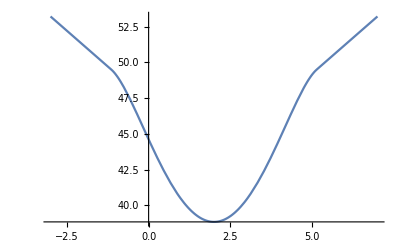

```mathematica
Plot[V1[z],{z,-3,7}]
```

```mathematica
NSol21[z_,a_,b_]:=y1[z]/.NDSolve[{{1/2 *σ0^2*y2'[x]+1/2 *δ2*σ0^2*(y2[x])^2+κ*(rbar-x)*y2[x]-λ*y1[x]+(x-rbar)^2==0,y2[a]==-k,y2[b]==l},{y1'[x]==y2[x]}},{y1,y2},{x,a,b}]
NSol22[z_,a_,b_]:=y2[z]/.NDSolve[{{1/2 *σ0^2*y2'[x]+1/2 *δ2*σ0^2*(y2[x])^2+κ*(rbar-x)*y2[x]-λ*y1[x]+(x-rbar)^2==0,y2[a]==-k,y2[b]==l},{y1'[x]==y2[x]}},{y1,y2},{x,a,b}]
```

```mathematica
Root2=FindRoot[{NSol21[avar,avar,bvar]-NSol21[alphavar,avar,bvar]==K+k(alphavar-avar),NSol21[bvar,avar,bvar]-NSol21[betavar,avar,bvar]==L-l(betavar-bvar),NSol22[alphavar,avar,bvar]==-k,NSol22[betavar,avar,bvar]==l},{{avar,delta0Sol[[3]]},{alphavar,delta0Sol[[4]]},{betavar,delta0Sol[[5]]},{bvar,delta0Sol[[6]]}},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->10,MaxIterations->1000]
```

NDSolve::ndsv: Cannot find starting value for the variable y1.

ReplaceAll::reps: {NDSolve[{{Plus[«2»]^2-0.06 y1[«1»]+0.2 Plus[«2»] y2[«1»]+0.0036 Power[«2»]+0.72 («1»)^(«1»)[«1»]==0,y2[avar]==-2,y2[bvar]==2},{y1'[x]==y2[x]}},{y1,y2},{x,avar,bvar}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndsv: Cannot find starting value for the variable y1.

ReplaceAll::reps: {NDSolve[{{Plus[«2»]^2-0.06 y1[«1»]+0.2 Plus[«2»] y2[«1»]+0.0036 Power[«2»]+0.72 («1»)^(«1»)[«1»]==0,y2[avar]==-2,y2[bvar]==2},{y1'[x]==y2[x]}},{y1,y2},{x,avar,bvar}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndsv: Cannot find starting value for the variable y1.

General::stop: Further output of NDSolve::ndsv will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{{Plus[«2»]^2-0.06 y1[«1»]+0.2 Plus[«2»] y2[«1»]+0.0036 Power[«2»]+0.72 («1»)^(«1»)[«1»]==0,y2[avar]==-2,y2[bvar]==2},{y1'[x]==y2[x]}},{y1,y2},{x,avar,bvar}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{avar→-1.152820169,alphavar→1.360949936,betavar→2.639050015,bvar→5.152820146}

```mathematica
a2=avar/.Root2; alpha2=alphavar/.Root2; beta2=betavar/.Root2; b2=bvar/.Root2;
```

```mathematica
V2[z0_]:=Module[{z=z0},
V[z1_]:=Piecewise[{{NSol21[alpha2,a2,b2]+K+k(alpha2-z1),z1<=a2},{NSol21[z1,a2,b2],a2<z1<b2},{NSol21[beta2,a2,b2]+L-l(beta2-z1),z1>=b2}}];
V[z]
]
```

```mathematica
Plot[{V0[z],V1[z],V2[z]},{z,-3,7},AxesLabel->{x,"Value function"}]
```

```mathematica
alpha2-a2
```

2.513770106

```mathematica
b2-beta2
```

2.51377013